```mathematica
sol = Solve[(x-2)(x-3)==0,x]
```

{{x→2},{x→3}}

```mathematica
ext = x/.sol
ext[[1]]
```

{2,3}

2

```mathematica
func = Cos[x]+x^2/. sol
```

{4+Cos[2],9+Cos[3]}

```mathematica
{4+Cos[2],9+Cos[3]}
```

```mathematica
Solve[2x+1==0,x]
```

{{x→-1/2}}

```mathematica
(2x+1) /. {x->-1/2}
```

0

```mathematica
(2x+1) /. {x->-2}
```

```mathematica
-3
Solve[Cos[y]==1/2,y]
```

{{y→ConditionalExpression[-π/3+2 π C[1],C[1]∈ℤ]},{y→ConditionalExpression[π/3+2 π C[1],C[1]∈ℤ]}}

```mathematica
sol = Solve[Cos[y]==1/2,y]
```

{{y→ConditionalExpression[-π/3+2 π C[1],C[1]∈ℤ]},{y→ConditionalExpression[π/3+2 π C[1],C[1]∈ℤ]}}

```mathematica
sol[[1]] /. C[1]->1
```

{y→(5 π)/3}

```mathematica
sol[[2]]/.C[1]->1
```

{y→(7 π)/3}

```mathematica
var1 = sol[[1]]/.C[1]->Range[-2,2]
```

{y→{-(13 π)/3,-(7 π)/3,-π/3,(5 π)/3,(11 π)/3}}

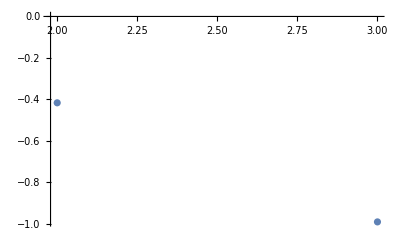

```mathematica
ListPlot[Partition[Riffle[x/.sol, Cos[x] /. sol],2]]
```

```mathematica
Solve[x^5+3x+1==0,x, Reals]//N
```

{{x→-0.331989}}

```mathematica
f[x_]:= x^2-2
dx = D[f[x],x]
```

2 x

```mathematica
sol = Solve[dx==0, x]
```

{{x→0}}

```mathematica
dxx=D[f[x],x,x]
```

2

```mathematica
dxx /. sol
```

{2}

```mathematica
Limit[Sign[dx],x->0, Direction ->-1]
```

1

```mathematica
Limit[Sign[dx],x->0, Direction ->1]
```

-1

```mathematica
Reduce[(x-2)(x+2)<0]
```

-2<x<2

```mathematica
Reduce[Cos[x]<0,x]
```

Reduce[Cos[x]<0,x]

```mathematica
(*исследуем функцию Sqrt[x]*ln[x]*)
```

```mathematica
func1[x_] := Sqrt[x]*Log[x]
```

```mathematica
FunctionDomain[func1[x], x]
```

```mathematica
x>0(*функция определена на х>0*)
```

```mathematica
FunctionRange[func1[x], x, y]
```

```mathematica
y≥-2/ⅇ(*функция ограничена снизу и принимает значения ≥-2/ⅇ*)
```

```mathematica
dx1 = D[func1[x], x]
```

```mathematica
1/(√x)+Log[x]/(2 √x)
sol1=Solve[dx1 ==0]
```

1/(√x)+Log[x]/(2 √x)

{{x→1/ⅇ^2}}

```mathematica
dxx1 = D[dx, x]
```

2

```mathematica
dxx1 /. sol1
```

{2}

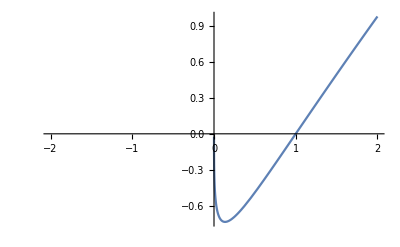

```mathematica
(*точка минимума 1/ⅇ^2*)
plt1 = Plot[func1[x], {x,-2,2}]
```

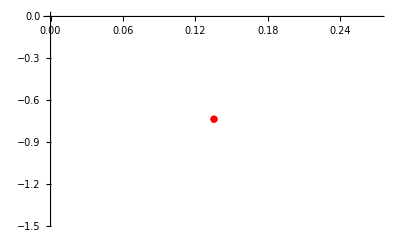

```mathematica
lplt1= ListPlot[Partition[Riffle[x/.sol1, func1[x] /. sol1],2], PlotStyle->Red]
```

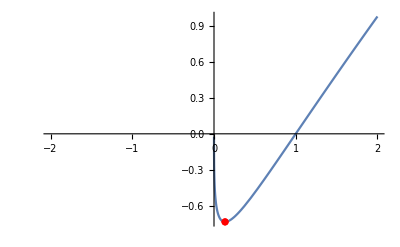

```mathematica
Show[plt1, lplt1]
```

```mathematica
(*точка минимума х=1/ⅇ^2*)
```

```mathematica
(*исследуем функцию Cos[x]+x*)
```

```mathematica
func2[x_]:= Cos[x]+x
```

```mathematica
FunctionDomain[func2[x], x]
```

```mathematica
True(*функция определена на всех вещественных числах*)
```

```mathematica
FunctionRange[func2[x], x, y]
```

```mathematica
True(*функция не ограничена, принимает все значения от -∞ до +∞*)
```

```mathematica
dx2=D[func2[x], x]
```

1-Sin[x]

```mathematica
sol2=Solve[dx2==0,x]
```

{{x→ConditionalExpression[π/2+2 π C[1],C[1]∈ℤ]}}

```mathematica
sol221 = sol2 /.C[1]->-1
sol222 = sol2 /.C[1]->0
sol223= sol2 /.C[1]->1
```

{{x→-(3 π)/2}}

{{x→π/2}}

{{x→(5 π)/2}}

```mathematica
dxx2 = D[dx2, x]
```

-Cos[x]

```mathematica
dxx2 /.sol22[[1]]
```

0

```mathematica
Limit[Sign[dx2],sol22[[1]], Direction->1]
```

1

```mathematica
Limit[Sign[dx2],sol22[[1]], Direction->-1]
```

1

```mathematica
(*производная не меняет знак, значит точки из списка - не экстремумы*)
```

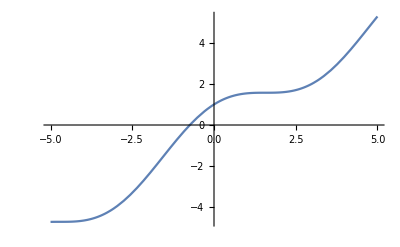

```mathematica
plt2 = Plot[func2[x], {x,-5,5}]
```

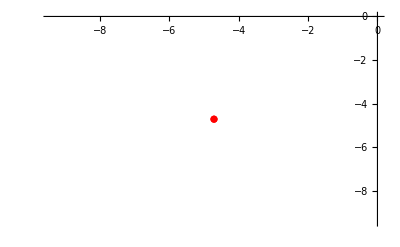

```mathematica
lplt21 = ListPlot[Partition[Riffle[x/.sol221, func2[x] /. sol221],2], PlotStyle->Red]
```

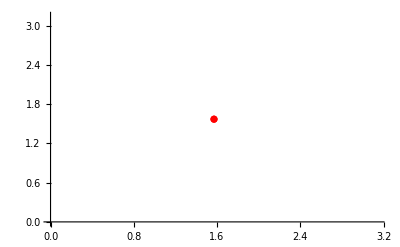

```mathematica
lplt22 = ListPlot[Partition[Riffle[x/.sol222, func2[x] /. sol222],2], PlotStyle->Red]
```

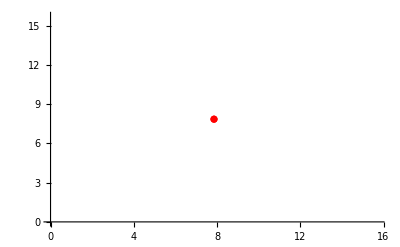

```mathematica
lplt23 = ListPlot[Partition[Riffle[x/.sol223, func2[x] /. sol223],2], PlotStyle->Red]
```

```mathematica
Show[plt2,lplt21, lplt22, lplt23]
```

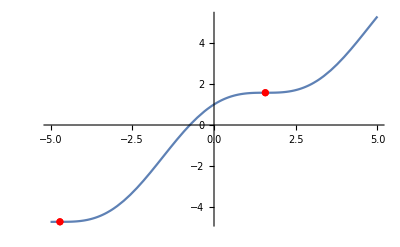

```mathematica
(*красные точки - перегибы*)
```

```mathematica
(*исследуем функцию (x-1)^4*)
```

```mathematica
func3[x_]:=(x-1)^4
```

```mathematica
FunctionDomain[func3[x],x]
```

```mathematica
True(*функция определена на всех вещественных числах*)
```

```mathematica
FunctionRange[func3[x],x,y]
```

```mathematica
y≥0(*функция ограничена снизу, принимает значения ≥0*)
```

```mathematica
dx3  = D[func3[x], x]
```

4 (-1+x)^3

```mathematica
sol3 = Solve[dx3 ==0]
```

{{x→1},{x→1},{x→1}}

```mathematica
x/.sol3
```

{1,1,1}

```mathematica
dxx3 = D[dx3, x]
```

12 (-1+x)^2

```mathematica
dxx3 /.sol3
```

{0,0,0}

```mathematica
Limit[Sign[dx3],sol3[[1]], Direction->1]
```

-1

```mathematica
Limit[Sign[dx3],sol3[[1]], Direction->-1]
```

1

```mathematica
(*первая производная меняет знак, точка 1 - точка минимума*)
```

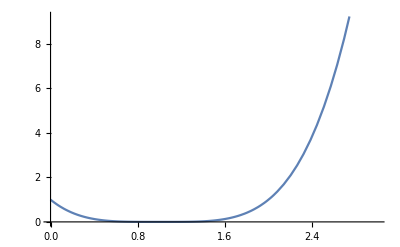

```mathematica
plt3 = Plot[func3[x], {x, 0,3}]
```

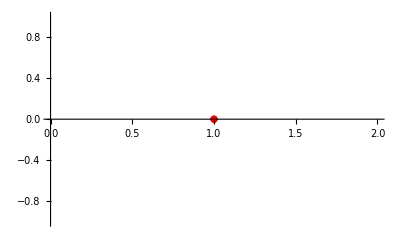

```mathematica
lplt3 = ListPlot[Partition[Riffle[x/.sol3, func3[x] /. sol3],2], PlotStyle->Red]
```

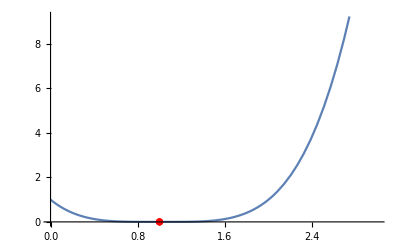

```mathematica
Show[plt3, lplt3]
```

```mathematica
(*точка минимума х=1*)
```

```mathematica
(*исследуем функцию (2x)/(1+x^2)*)
func4[x_]:=(2x)/(1+x^2)
```

```mathematica
FunctionDomain[func4[x], x]
```

```mathematica
True(*функция определена на всех вещественных числах*)
```

```mathematica
FunctionRange[func4[x],x,y]
```

```mathematica
-1≤y≤1(*функция ограничена сверху и снизу, принимает значения от -1 до 1*)
```

```mathematica
dx4= D[func4[x], x]
```

-(4 x^2)/((1+x^2)^2)+2/(1+x^2)

```mathematica
sol4 = Solve[dx4==0]
```

{{x→-1},{x→1}}

```mathematica
x/.sol4
```

{-1,1}

```mathematica
dxx4=D[dx4,x]
```

(16 x^3)/((1+x^2)^3)-(12 x)/((1+x^2)^2)

```mathematica
dxx4 /. sol4
```

{1,-1}

```mathematica
(*вторая производная ≠0, точка минимума -1 и точка максимума 1*)
```

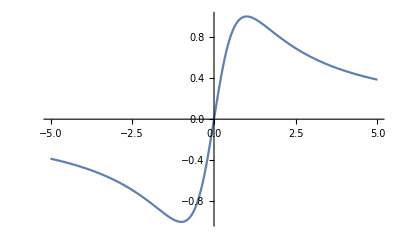

```mathematica
plt4 = Plot[func4[x], {x, -5, 5}]
```

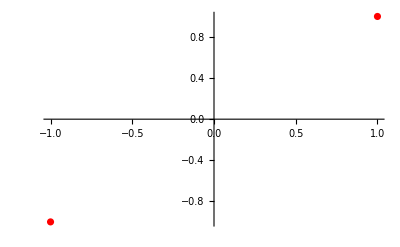

```mathematica
lplt4 = ListPlot[Partition[Riffle[x/.sol4, func4[x] /. sol4],2], PlotStyle->Red]
```

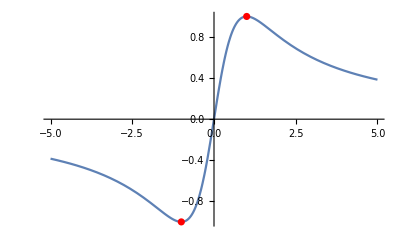

```mathematica
Show[plt4,lplt4]
```

```mathematica
(*точка минимума х=-1 и точка максимума х=1*)
```